# Pappus Graph

The Pappus graph is a bipartite 3-regular undirected graph with 18 vertices and 27 edges.

Mengyi Shan, Jun. 27,  2018

Pappus Graph is an interesting and inspiring example in the mathematical field of graph theory. It is a cubic symmetric distance-regular graph on 18 vertices, and it’s also the incidence graph of the  9_3 configuration appearing in Pappus’s hexagon theorem, namely the Pappus configuration. We attempt to approach Pappus Graph with its properties as a graph, properties related to algebraic structures, and relationship with Euclidean and projective geometry.

## Graphic Properties

Let’s start with the basic and the most common form of Pappus Graph.

Get the data of Pappus Graph and draw its basic form:

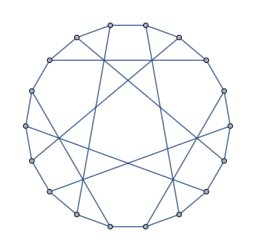

```mathematica
g=GraphData["PappusGraph"]
```

The number of edges is 27, and the number of vertices is 18.

Get the count of vertices and edges

```mathematica
{VertexCount[g], EdgeCount[g]}
```

{18,27}

### Basic Properties

Here are a few basic properties of the Pappus Graph that can be answered with true or false.

Show a few basic graphic properties of the Pappus Graph. Choose properties in the popup menu to see the result:

```mathematica
ActionMenu["Basic Properties",{"Empty?":>Print[EmptyGraphQ[g]],"Complete?":>Print[CompleteGraphQ[g]],"Connected?":>Print[ConnectedGraphQ[g]],"Directed?":>Print[DirectedGraphQ[g]],"Simple?":>Print[SimpleGraphQ[g]],"Weighted?":>Print[WeightedGraphQ[g]]},Appearance->"PopupMenu",ImageSize->{200,40},ImageMargins->Automatic,FrameMargins->10]
```

Basic Properties

### Eulerian and Hamiltonian

Although Pappus Graph is not Eulerian, which means there’s no way to find a cycle that traverses every edge exactly once

Check if it’s Eulerian:

```mathematica
EulerianGraphQ[g]
```

False

It is indeed Hamiltonian, which means there is some way to find a cycle that traverses every vertex exactly once.

Check if it’s Hamiltonian:

```mathematica
HamiltonianGraphQ[g]
```

True

We can find that cycle and visualize it.

Find the Hamiltonian cycle:

```mathematica
hcycle=First[FindHamiltonianCycle[g]]
```

{1<->4,4<->8,8<->5,5<->6,6<->9,9<->12,12<->11,11<->14,14<->17,17<->2,2<->16,16<->13,13<->10,10<->7,7<->3,3<->18,18<->15,15<->1}

Use animation to visualize the Hamiltonian cycle:

```mathematica
Animate[HighlightGraph[g,PathGraph[hcycle[[1;;n]]],GraphHighlightStyle->"Thick"],{n,0,Length[hcycle],1}]
```

### Chromatic Number

The chromatic number of a graph is the smallest number of colors needed to color the vertices of G so that no two adjacent vertices share the same color, i.e., the smallest value of k possible to obtain a k-coloring. The chromatic number of Pappus Graph is 2.

Get a minimum vertex (2 in this case) method to color the vertices:

```mathematica
cols=GraphData["PappusGraph","MinimumVertexColoring"]
```

{1,1,2,2,2,1,1,1,2,2,2,1,1,1,2,2,2,1}

And it’s easy to visualize all vertices with 2-coloring.

Draw a graph to show the coloring:

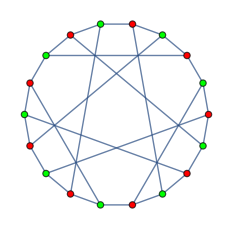

```mathematica
HighlightGraph[GraphData["PappusGraph"],MapIndexed[Style[#2[[1]],{Red,Green}[[#]]]&,cols],VertexSize->Medium]
```

A graph is bipartite if its vertices can be divided into two groups and all edges are between the groups. Pappus Graph seems quite different from normal bipartite graphs, but it is indeed bipartite. With the 2-coloring example above, it’s easy to see that all edges are between one red vertex and one green vertex.

Check if it’s bipartite:

```mathematica
BipartiteGraphQ[g]
```

True

A similar problem is edge chromatic numbers.

Get a minimum edge (3 in this case) method to color the vertices:

```mathematica
cols=GraphData["PappusGraph","MinimumEdgeColoring"]
```

{1,2,3,1,2,3,1,2,3,3,2,2,3,3,1,1,1,2,3,2,2,3,3,1,1,1,2}

And its visualization.

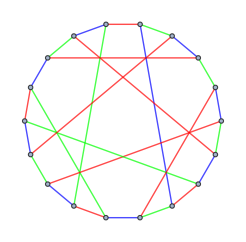

```mathematica
With[{g="PappusGraph"},With[{edges=GraphData[g,"EdgeSet"]},HighlightGraph[GraphData[g],MapIndexed[Style[edges[[#2[[1]]]],{Red,Green,Blue}[[#]]]&,cols]]]]
```

## Algebraic Properties

### Matrices

An adjacency matrix is also known as a connectivity matrix. An entry a_ij of the adjacency matrix is the number of directed edges from vertex ν_i to vertex ν_j. The output is in the form of a sparse array.

Get the adjacency matrix of Pappus Graph:

```mathematica
AdjacencyMatrix[g]
```

SparseArray[<54>, {18, 18}]

We can turn it into matrix form by normalization, and make a matrix plot based on the matrix.

Use MatrixPlot to visualize:

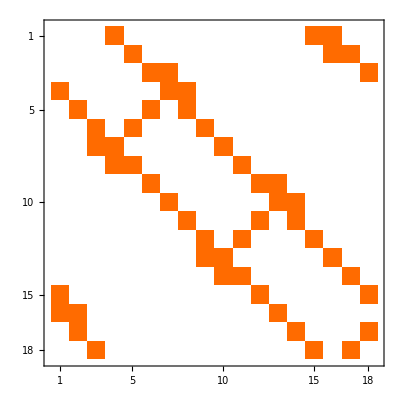

```mathematica
MatrixPlot[Normal[AdjacencyMatrix[g]]]
```

Similarly, a Kirchhoff matrix also shows the relationship between vertices. The diagonal entries k_(i,i) equal the degree of v_i. An entry k_(i,j) is -1 if vertex v_i is adjacent to v_j. The output is in the form of a sparse array.

Get the Kirchhoff matrix of Pappus Graph:

```mathematica
KirchhoffMatrix[g]
```

SparseArray[<72>, {18, 18}]

We can turn it into matrix form by normalization, and make a matrix plot based on the matrix. By examining the difference between the Kirchhoff matrix and the normal adjacency matrix, we could see that the orange areas represent a node connected to itself.

Use MatrixPlot to visualize:

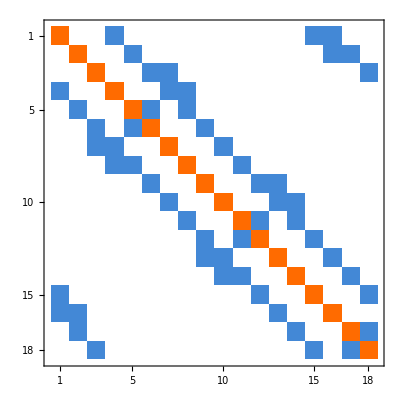

```mathematica
MatrixPlot[Normal[KirchhoffMatrix[g]]]
```

An incidence matrix, on the other hand, can also be calculated and visualized by matrix plot.

Use Matrix Plot to visualize incidence matrix:

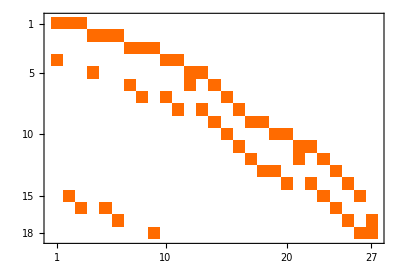

```mathematica
MatrixPlot[Normal[IncidenceMatrix[g]]]
```

Distance matrix is used to show distance between each two points. We can observe similar pattern of adjacency matrix in the plot of distance matrix.

Use Matrix Plot to visualize distance matrix:

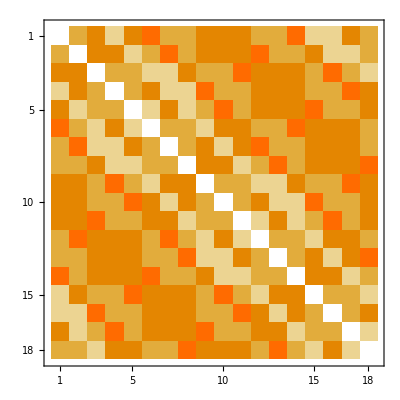

```mathematica
MatrixPlot[GraphDistanceMatrix[g]]
```

### Spectrum

The set of graph eigenvalues of the adjacency matrix is called the spectrum of the graph. For Pappus Graph, we can check the data of its spectrum which is stored in Wolfram Language.

Get the list of spectrum of Pappus Graph as data stored in the language.

```mathematica
GraphData["PappusGraph","Spectrum"]
```

{-3,-√3,-√3,-√3,-√3,-√3,-√3,0,0,0,0,√3,√3,√3,√3,√3,√3,3}

Or we can also directly calculate the eigenvalues. And we’ll get the same answer.

Another way is, by definition, directly calculating the eigenvalues.

```mathematica
Eigenvalues[AdjacencyMatrix[g]]
```

{-3,3,-√3,-√3,-√3,-√3,-√3,-√3,√3,√3,√3,√3,√3,√3,0,0,0,0}

Similarly, we can get the characteristic polynomial that has the eigenvalues as roots.

Get the characteristic polynomial of Pappus Graph:

```mathematica
CharacteristicPolynomial[AdjacencyMatrix[g],x]
```

-6561 x^4+13851 x^6-12393 x^8+6075 x^10-1755 x^12+297 x^14-27 x^16+x^18

Factorize it to see that its roots are indeed the eigenvalues.

```mathematica
Factor[-6561 x^4+13851 x^6-12393 x^8+6075 x^10-1755 x^12+297 x^14-27 x^16+x^18]
```

(-3+x) x^4 (3+x) (-3+x^2)^6

Two nonisomorphic graphs can share the same graph spectrum, i.e., have the same eigenvalues of their adjacency matrices. Such graphs are called cospectral. Determining which graphs are uniquely determined by their spectra is in general a very hard problem.

Check if Pappus Graph is determined by spectrum:

```mathematica
GraphData["PappusGraph","DeterminedBySpectrum"]
```

True

Thus there’s no cospectral graphs:

```mathematica
GraphData["PappusGraph","CospectralGraphs"]
```

{}

### Other Properties

The numerically second smallest eigenvalue (counting multiple eigenvalues separately) of the Laplacian matrix of a graph G is known as the algebraic connectivity of the graph. This eigenvalue is greater than 0 iff G is a connected graph.

Calculate the second smallest eigenvalue as the algebraic connectivity:

```mathematica
RankedMin[DeleteDuplicates[Eigenvalues[GraphData["PappusGraph","LaplacianMatrix"]]],2]
```

3-√3

Directly get the algebraic connectivity from GraphData to check if they’re the same:

```mathematica
GraphData["PappusGraph","AlgebraicConnectivity"]
```

3-√3

Chromatic polynomial counts the number of graph colorings as a function of the number of colors. The chromatic polynomial of Pappus Graph is:

Get the chromatic polynomial of Pappus Graph.

```mathematica
ChromaticPolynomial[g,x]
```

-356509 x+2046915 x^2-5679480 x^3+10226049 x^4-13475745 x^5+13848696 x^6-11514312 x^7+7913106 x^8-4546083 x^9+2191329 x^10-883818 x^11+295614 x^12-80712 x^13+17550 x^14-2925 x^15+351 x^16-27 x^17+x^18

Get the value of chromatic function when x is small integers:

```mathematica
{RadioButtonBar[Dynamic[x],Range[10]],Dynamic[ChromaticPolynomial[g,x]]}
```

{ | 1   | 2   | 3   | 4   | 5   | 6   | 7   | 8   | 9   | 10,}

The automorphism group of the Pappus graph is a group of order 216. It acts transitively on the vertices, on the edges and on the arcs of the graph. Therefore the Pappus graph is a symmetric graph. It has automorphisms that take any vertex to any other vertex and any edge to any other edge.

Check if it is symmetric.

```mathematica
GraphData["PappusGraph","Symmetric"]
```

True

Get the automorphism group and check its order:

```mathematica
GraphData["PappusGraph","AutomorphismGroup"]
```

PermutationGroup[{Cycles[{{2,13},{4,15},{5,9},{7,18},{8,12},{10,17}}],Cycles[{{2,18},{3,5},{7,8},{10,11},{12,13},{15,16}}],Cycles[{{2,12},{3,10},{5,11},{6,14},{9,17},{13,18},{15,16}}],Cycles[{{1,2},{4,5},{6,7},{9,10},{12,14},{15,17}}],Cycles[{{1,3},{2,9},{4,7},{5,13},{6,16},{8,10},{11,14},{12,17},{15,18}}]}]

```mathematica
GroupOrder[GraphData["PappusGraph","AutomorphismGroup"]]
```

216

Draw the Cayley Graph based on the group (actually hard to visualize since 216 is too large):

```mathematica
CayleyGraph[%43]
```

-Graphics-

## Basic Form and Variations

Here’s the basic and the most common form of Pappus Graph.

Draw a basic form of Pappus Graph:

```mathematica
g=GraphData["PappusGraph"]
```

-Graphics-

With the same number of edges and vertices, we can find several different version of Pappus Graph. For example, the canonical form of Pappus graph.

Draw the canonical form of Pappus Graph:

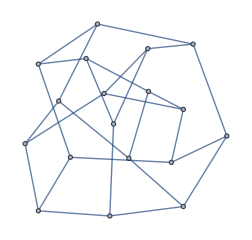

```mathematica
GraphData["PappusGraph","CanonicalGraph"]
```

```mathematica
GraphData["PappusGraph","Edges"]
```

Many, many other variations stored in the Wolfram Language.

Draw all other forms of Pappus Graph stored in the data set.

```mathematica
GraphData["PappusGraph","AllImages"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

And even 3D Pappus Graph.

Draw a 3D Pappus Graph.

```mathematica
GraphData["PappusGraph","Graph3D"]
```

-Graphics3D-

In line graph, Each vertex corresponds to an edge in the original graph. Two vertices are adjacent if their corresponding edges share a common vertex.

Draw the line graph of Pappus Graph.

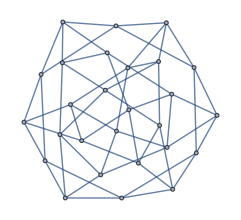

```mathematica
LineGraph[g]
```

```mathematica
{EdgeCount[LineGraph[g]],VertexCount[LineGraph[g]]}
```

{54,27}

We can try to randomly generate graphs, but the lengths of edges may not the the same as Pappus Graph.

Randomly generate graphs with the same number of vertices and same degree as Pappus Graph, but it’s not Pappus Graph.

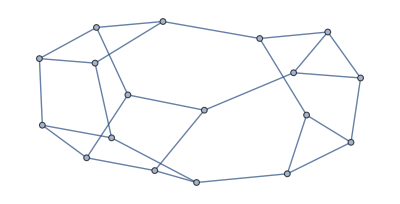

```mathematica
RandomGraph[DegreeGraphDistribution[ConstantArray[3,VertexCount[g]]]]
```

## Special Case: Pappus Configuration

Now we introduce the concept of incidence graph. Incidence graph of an original graph is a bipartite graph with all vertices of the original graph as “black vertices”, and all edges of the original graph as “white vertices”.

Pappus Graph is the incidence graph of Pappus configuration.

```mathematica
Import["http://mathworld.wolfram.com/images/eps-gif/PappusTheorem_1000.gif"]
```

-Graphics-

### Pappus Hexagon Theorem

Theorem: Let A, B, C be three points on a straight line and let X, Y, Z be three points on another line. If the lines AY , BZ, CX intersect the lines BX, CY , AZ, respectively then the three points of intersection are collinear.

```mathematica
Clear[x]
```

An animation to illustrate Pappus Theorem:

```mathematica
Module[{solcross},
Quiet[solcross[{a_,b_},{c_,d_}]:=Evaluate[Solve[{x,y}∈Line[{{a[[1]],a[[2]]},{b[[1]],b[[2]]}}]&&{x,y}∈Line[{{c[[1]],c[[2]]},{d[[1]],d[[2]]}}],{x,y}][[1,;;,2,1]]]];

DynamicModule[{pts={{-7,4},{5,7},{-8,-2},{8,-5},{0.2,5.8},{-3.2,-2.9}}},
LocatorPane[Dynamic[pts,(pts=#[[;;4]]~Join~{#[[1]]+Clip[(#[[5]]-#[[1]]).(#[[2]]-#[[1]])/Norm[#[[2]]-#[[1]]]^2,{0,1}](#[[2]]-#[[1]]),#[[3]]+Clip[(#[[6]]-#[[3]]).(#[[4]]-#[[3]])/Norm[#[[4]]-#[[3]]]^2,{0,1}](#[[4]]-#[[3]])})&],Graphics[{{Line[{{#1,#2},{#3,#4}}],Line[{{#1,#6},{#3,#5},{#5,#4},{#2,#6},{#1,#4},{#2,#3}}]}&@@Array[Dynamic[pts[[#]]]&,Length@pts],Darker@Green,Dynamic[With[{c1=solcross[{#1,#6},{#3,#5}],c2=solcross[{#5,#4},{#2,#6}],c3=solcross[{#1,#4},{#2,#3}]},{Line[{c1,c2}],Red,PointSize@.02,Point[{c1,c2,c3}]}]&@@pts]},PlotRange->{{-10,10},{-7,10}}],{{-10,-10},{10,10}},Appearance->(Graphics/@Catenate[ConstantArray@@@{{{PointSize@.02,Point[{0,0}]},4},{{PointSize@.02,Point[{0,0}]},2}}])]
]]
```

In its earliest known form, Pappus’s Theorem is Propositions 138, 139, 141, and 143 of Book VII of Pappus’s Collection. It shows the beauty of simplicity in projective geometry, and was still studied by mathematicians nowadays. Here we want to provide a proof to Pappus Hexagon Theorem.

#### Proof : Determinant Cancellation

The main algebraic tool used in this section are homogeneous coordinates.

```mathematica
Import["http://mathworld.wolfram.com/images/eps-gif/PappusTheorem_1000.gif"]
```

-Graphics-

We use (x, y, z) coordinates to represent each vertex.

```mathematica
Insert[Grid[{{"point","x","y","z"},{A,1,0,0},{B,a,b,c},{C,d,e,f},{D,0,1,0},{E,t,h,i},{F,j,k,l},{X,0,0,1},{Y,m,n,o},{Z,p,q,r}},Dividers->{{True,True,False,False,True},True}],{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

point | x | y | z
A | 1 | 0 | 0
B | a | b | c
C | d | e | f
D | 0 | 1 | 0
ⅇ | t | h | i
F | j | k | l
X | 0 | 0 | 1
Y | m | n | o
Z | p | q | r

By the property of colinear, we can get the following equations:

```mathematica
Insert[Grid[{{"[1,2,3]= 0 → ce = bf"},{"[1,5,9]= 0 → iq = hr"},{"[1,6,8]= 0 → ko = ln"},{"[2,4,9]= 0 → ar = cp"},{"[3,4,8]= 0 → fm = do"},{"[3,5,7]= 0 → dh = eg"},{"[4,5,6]= 0 → gl = ij"}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

[1,2,3]= 0 → ce = bf
[1,5,9]= 0 → iq = hr
[1,6,8]= 0 → ko = ln
[2,4,9]= 0 → ar = cp
[3,4,8]= 0 → fm = do
[3,5,7]= 0 → dh = eg
[4,5,6]= 0 → gl = ij

And we can show:

```mathematica
"mq=np→ [7,8,9]=0"
```

mq=np→ [7,8,9]=0

A Glimpse Into Projective Geometry

An interesting property of Pappus Hexagon Theorem is that it is self-dual. That is, the theorem is also valid for the dual graph.

```mathematica
Import["https://www.researchgate.net/profile/Serge_Tabachnikov/publication/305401152/figure/fig3/AS:499754473713667@1496162160041/Dual-Pappus-theorem.png"]
```

-Graphics-

The Duality Principle is a typical feature for Projective Geometry. As an important part of mathematics, Projective Geometry is the study of geometric properties that are invariant with respect to projective transformations.

Pappus Theorem was the first geometrical properties of a projective nature, discovered during the 3rd century by Pappus of Alexandria. Pappus Theorem has been generalized by B. Pascal (1623-1662) who proved that the points may be taken on a conic section instead of two straight lines.

```mathematica
Entity["Person","Pappus::zbtf6"][EntityProperty["Person","MathematicalAchievements"]]
```

{honeycomb conjecture,irrationality of Sqrt[2],Pythagoras’s constant,ellipse,hyperbola,parabola,Pappus graph}

It's fair to say that on the base of Pappus Theorem, the whole brilliant world of Projective Geometry is built.

## Further explorations

Projective Geometry

Pascal’s Theorem and Brianchon’s theorem.

Bouwer Graph

## Author contact information

Mengyi Shan

Claremont CA, United States

Harvey Mudd College ’21

mshan@hmc.edu